```mathematica
Quiet@Remove["Global`*"];
```

(-a+π)^2/(-1+a π)^2+((1-π^2)^2)/(-1+a π)^2

x = 1.67884 y= -0.21608

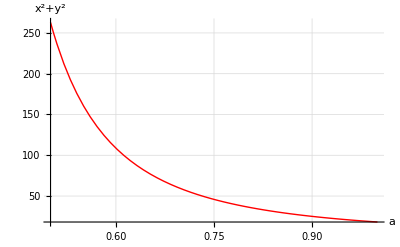

```mathematica
sol = Solve[{a*x + y == Pi, x + Pi*y == 1}, {x,y}][[1]];
exprtodraw = x^2+y^2/.sol
a = 2.;
Print["x = ", x/.sol," y= ", y/.sol]
Plot[exprtodraw, {a, 0.5, 1},AxesLabel->{"a", "x^2+y^2"}, GridLines->Automatic, PlotStyle->{Red, Thick}]
```

```mathematica
Quiet@Remove["Global`*"];
```

{y[t]→1/2 ⅇ^(-t-t^2/2) (-2+2 ⅇ^(t+t^2/2)+√((2 π)/ⅇ) Erfi[1/(√2)]-√((2 π)/ⅇ) Erfi[(1+t)/(√2)])}

1/2 ⅇ^(-t-t^2/2) (-2+2 ⅇ^(t+t^2/2)+√((2 π)/ⅇ) Erfi[1/(√2)]-√((2 π)/ⅇ) Erfi[(1+t)/(√2)])

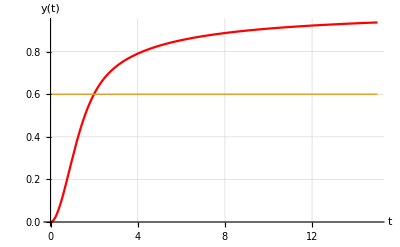

```mathematica
eqn = {y'[t] + (t+1)*y[t] == t, y[0] == 0};
sol = DSolve[eqn, y[t], t][[1]]
result = y[t]/.sol
Plot[{result,0.6}, {t, 0, 15}, AxesLabel->{"t", "y(t)"}, GridLines->Automatic, PlotStyle->{Red, Thick}]
```

```mathematica
t0 = t/.FindRoot[{result == 0.6}, {t, 2}]
Print["t0 = ", t0]
```

1.99083

t0 = 1.99083